# Fit vertex angles in experiments, measure domain sizes, and the number of vertices (corners) of each domain

[MinD] = 2.5 µM
[MinE-His] = 7 µM

```mathematica
img=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180427_ch3_2.5uM-MinD_7uM-E-His_snap01.lsm"];
```

```mathematica
img2=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180427_ch3_2.5uM-MinD_7uM-E-His_snap02.lsm"];
```

Separate MinD and MinE channels

```mathematica
imgSep=ColorSeparate[img];
imgSep2=ColorSeparate[img2];
```

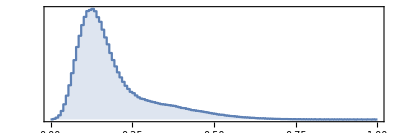
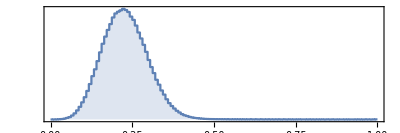

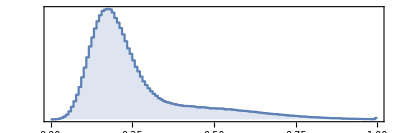
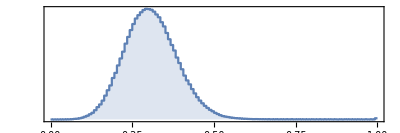

```mathematica
ImageHistogram/@ImageAdjust/@imgSep
ImageHistogram/@ImageAdjust/@imgSep2
```

```mathematica
imgReg={ImageAdjust[ImageAdjust@imgSep[[1]],0,{0,0.6}],ImageAdjust@imgSep[[2]]};
imgReg2={ImageAdjust[ImageAdjust@imgSep2[[1]],0,{0,0.8}],ImageAdjust@imgSep2[[2]]};
```

```mathematica
colorMap={minD,minE,minE+minD/1.5};
```

Image 1, Extended Data Fig. 1d

```mathematica
imgColor=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg))
```

Image 2, Extended Data Fig. 1d

```mathematica
imgColor2=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg2))
```

## Image preparation

### MinD-MinE pixel clustering (using first image)

```mathematica
classImage=BrightnessEqualize[ImageAdjust[#]]&/@imgSep;
```

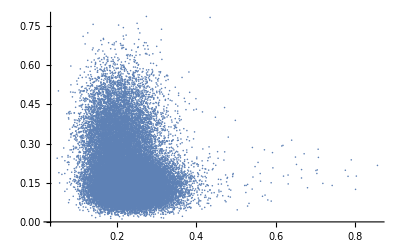

```mathematica
ListPlot[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}[[All,;;200,;;200]]],PlotRange->All]
```

```mathematica
clusters=FindClusters[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}],2,Method->"KMeans",DistanceFunction->EuclideanDistance];
```

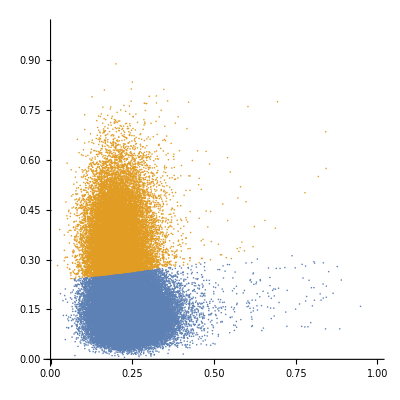

```mathematica
ListPlot[clusters[[All,;;;;10]],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

```mathematica
centroids=Mean/@clusters;
```

```mathematica
ratioDE=#[[1]]/#[[2]]&@First@Differences[centroids]
```

-0.121317

### Mesh binarization

```mathematica
ClearAll@meshBinarize;
Options[meshBinarize]={"ThresholdPixelNumber"->10};
meshBinarize[img_,ratioDE_,opts:OptionsPattern[]]:=Block[
{imgEq=BrightnessEqualize[ImageAdjust[#]]&/@img,
minDMeas,
minE,
minD,
imgProj,
imgBinarized,
morphImg,
smallComponents,
morphMask,
imgBinarizedCleaned
},
minDMeas=ImageMeasurements[imgEq[[2]],{"Mean","StandardDeviation"}];
minE=imgEq[[1]];
(*to ignore MinD aggregates, cut brightness at mean+std off*)
minD=ImageClip[imgEq[[2]],{0,Total@minDMeas}];
(*project pixel MinD MinE fluorescence values on the axis connecting the centroids of the clusters identified in the initial image*)
imgProj=Image[ImageData[minE]+ratioDE ImageData[minD]];
(*binarize along this axis, and smooth to get a connected mesh*)
imgBinarized=Binarize[GaussianFilter[Binarize[ImageAdjust@imgProj],5],0.3];

(*remove too small morphological components*)
morphImg=MorphologicalComponents[imgBinarized];
smallComponents=Keys@Select[ComponentMeasurements[morphImg,"Area"],#[[2]]<10&];
morphMask=Clip[morphImg/.Thread[smallComponents->-1],{-1,0}];
imgBinarizedCleaned=Image[ImageData[imgBinarized]+morphMask];

{imgProj,imgBinarizedCleaned}
]
```

```mathematica
imgProj=meshBinarize[imgSep,ratioDE];
```

```mathematica
imgProj2=meshBinarize[imgSep2,ratioDE];
```

Skeleton of the network

```mathematica
branchIm=Thinning[imgProj[[2]]]
```

-Graphics-

```mathematica
branchIm2=Thinning[imgProj2[[2]]];
```

## Analysis

### Measurement functions

Fit the vertex by assuming Gaussian cross-sections of the vertex arms:

```mathematica
ClearAll@lossF;
lossF[vertexData_,x1_?NumericQ,x2_?NumericQ,angles_?VectorQ]:=
Total[
Function[d,
(d[[3]]-Exp[-#/((width/2)^2/Log[2])])^2&@Min[If[Length@#==0,{1000},#]&@((Norm[d[[{1,2}]]-{x1,x2}]^2-((d[[{1,2}]]-{x1,x2}).{Cos[#],Sin[#]})^2)&/@
Select[angles,
Function[angle,((d[[{1,2}]]-{x1,x2}).{Cos[angle],Sin[angle]})>-10^-10]
])
]]/@vertexData[[2]]];
```

```mathematica
ClearAll@measureData;
measureData[vertexData_,armNumber_]:=
Block[
{
dataW,
iniCond,
iniCondClean,
vars,
sol,sol2,
fitSuccess=1,
fit
},
(*get initial conditions for the angles of the vertex arms by making a radial histogram and finding its peaks*)
dataW=WeightedData[#[[All,1]],#[[All,2]]]&@({PlanarAngle[{0,0}->{{1,0},#[[{1,2}]]}],#[[3]]}&/@Transpose[{vertexData[[2,All,1]],vertexData[[2,All,2]],Rescale@vertexData[[2,All,3]]}]);
iniCond=If[#[[1]]>Pi,{#[[1]]-2Pi,#[[2]]},#]&/@({0.05+(HistogramList[dataW,{0,2Pi,0.2}][[1,#[[1]]]]),#[[2]]}&/@(FindPeaks[Last@HistogramList[dataW,{0,2Pi,0.2}],1,0,0,Padding->"Periodic"]));
(*take mean of peaks that lie close together; map angles onto [-Pi,Pi] range*)
iniCondClean=If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&/@
SortBy[DeleteDuplicates@Table[
Mean[
Select[Join[iniCond,{#[[1]]-2Pi,#[[2]]}&/@iniCond,{#[[1]]+2Pi,#[[2]]}&/@iniCond],Min[Abs[#[[1]]-ini[[1]]]<0.5&]]
],{ini,iniCond}],#[[2]]&][[All,1]];
If[Length[iniCondClean]<3,
sol=I,
iniCond=iniCondClean[[-armNumber;;]];
vars=Symbol["a"<>ToString[#]]&/@Range[Length@iniCond];
Quiet@Check[sol=Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2];,fitSuccess=0;];
(*Try a second time if it failed*)
If[fitSuccess==0,
sol2=Check[Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2,Method->"PrincipalAxis"],I];
sol=sol2;
];
];
If[sol===I,
I,
fit=Join[{vertexData[[1,1]]+x1,vertexData[[1,2]]+x2}/.sol,Sort[If[#<-Pi,#+2Pi,If[#>Pi,#-2Pi,#]]&/@(vars/.sol)]];
If[Min[Abs@Differences[fit[[2;;]]]]<0.01,
I,
fit]
]
];
```

## Determine branch points

The branch width is about 3 pixels, see below.
We prun branches shorter than 10 pixels because for their vertices no reliable angles can be determined (repeatedly to account for short, branched segments that we want to remove).

```mathematica
branchImPrun=Thinning[Pruning[Pruning[Pruning[branchIm,10],10],10]]
```

-Graphics-

```mathematica
branchPoints=MorphologicalBranchPoints[Binarize@branchImPrun];
```

```mathematica
branchPointCoords=ImageValuePositions[branchPoints,1];
```

```mathematica
HighlightImage[branchImPrun,{AbsolutePointSize[3],branchPointCoords}]
```

-Graphics-

```mathematica
branchImPrun2=Thinning[Pruning[Pruning[Pruning[branchIm2,10],10],10]];
branchPoints2=MorphologicalBranchPoints[Binarize@branchImPrun2];
branchPointCoords2=ImageValuePositions[branchPoints2,1];
```

## Average branch widths (using first image)

Determine average branch width by binarizing the experimental network image (imgProj[[1]]) at half-maximum intensity, count the white pixels (width*length of network) and divide by the white pixels in the network skeleton (length of network because everywhere only one pixel wide)

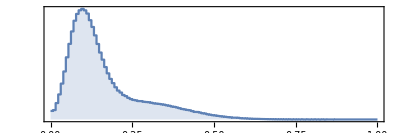

```mathematica
ImageHistogram[imgProj[[1]]]
```

Set 0.45 as branch intensity maximum and 0.1 as intensity minimum (intensity of plateaus)

```mathematica
width=N@Total@Flatten@ImageData[Binarize[ImageAdjust[imgProj[[1]],0,{0.1,0.45}],0.5]]/(Total@Flatten@ImageData@branchIm)
```

3.26315

## Vertices - Image 1

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords,0.]]}]/@branchPointCoords,#[[-1]]>10&];
Length@tripleVerticesRaw
```

1249

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices=Block[{
tvs=tripleVerticesRaw,
branches=branchImPrun,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices
```

1249

### 4-fold vertices

```mathematica
quadrupleVerticesRaw=Complement[branchPointCoords,tripleVertices[[All,1]]];
quadrupleVertices=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw],I];
Length@quadrupleVertices
```

228

```mathematica
vertices=Join[tripleVertices,quadrupleVertices];
```

```mathematica
HighlightImage[branchIm,{AbsolutePointSize[3],tripleVertices,AbsolutePointSize[6],quadrupleVertices}]
```

-Graphics-

## Analysis of triple vertices - Image 1

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

1249

```mathematica
failedVertices
```

{}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
Show[
HighlightImage[imgProj[[1]],{AbsolutePointSize[5],tripleVertices}],
Graphics[Join[{Darker@Red,Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{255,150,20}/255]},
Circle[#,3]&/@quadrupleVertices]]
]
```

-Graphics-

```mathematica
angles3=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

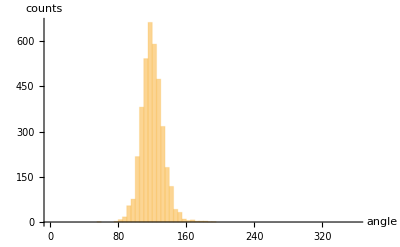

```mathematica
Histogram[{
Flatten[angles3,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles3,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles3,1]]
```

12.7774

#### FitList

```mathematica
vertex3MeasurementsRaw
```

### Fit result

```mathematica
Show[
imgColor,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices]]
]
```

## Vertices - Image 2

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw2=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords2,0.]]}]/@branchPointCoords2,#[[-1]]>10&];
Length@tripleVerticesRaw2
```

841

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices2=Block[{
tvs=tripleVerticesRaw2,
branches=branchImPrun2,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices2
```

840

### 4-fold vertices

```mathematica
quadrupleVerticesRaw2=Complement[branchPointCoords2,tripleVertices2[[All,1]]];
quadrupleVertices2=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw2[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw2],I];
Length@quadrupleVertices2
```

97

```mathematica
vertices2=Join[tripleVertices2,quadrupleVertices2];
```

```mathematica
HighlightImage[branchIm2,{AbsolutePointSize[3],tripleVertices2,AbsolutePointSize[6],quadrupleVertices2}]
```

-Graphics-

## Analysis of triple vertices - Image 2

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj2[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices2}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw2=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw2],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw2],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw2,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

840

```mathematica
failedVertices
```

{}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
angles32=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

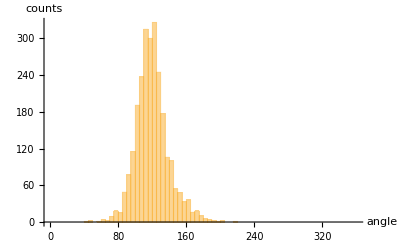

```mathematica
Histogram[{
Flatten[angles32,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles32,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles32,1]]
```

19.0492

#### FitList

```mathematica
vertex3MeasurementsRaw2
```

{{645.549,994.878,-1.76535,0.428279,2.71716},{779.116,988.652,-2.9812,-1.13967,0.506626},{31.5485,985.938,-1.37687,0.363095,2.21695},{402.35,985.891,-0.895447,0.97057,2.93073},{892.498,986.504,-1.02377,0.743557,2.69699},{83.6074,985.242,-0.467214,1.04076,2.75283},{754.116,984.458,-2.21798,0.156259,2.15232},{204.544,982.363,-1.1736,0.789846,2.60971},{462.748,981.617,-2.6896,-0.0600839,1.87313},{480.717,980.,-1.1291,1.02594,3.01982},{344.094,979.15,-1.75431,0.164668,1.99235},{449.676,975.84,-2.26817,0.377944,2.22367},{641.244,974.655,-2.92724,-0.946977,1.35288},{411.506,974.499,-2.16192,-0.237935,2.25215},{715.67,974.584,-2.9989,-1.00252,1.66084},{99.7024,972.983,-2.25734,-0.44645,2.38873},{373.252,970.482,-1.67788,0.778642,2.52384},{128.87,970.577,-2.64644,-0.68872,1.49905},{852.039,968.822,-1.556,0.512335,2.39346},{549.502,967.493,-2.49784,-0.336714,1.91376},{960.96,965.784,-2.27271,-0.433244,1.7503},{441.349,964.614,-1.66552,0.998802,2.75125},{116.835,964.457,-1.4177,0.462875,2.64418},{723.665,962.504,-2.01236,0.315521,2.17914},{307.492,961.49,-2.20697,0.475311,2.20121},{158.262,958.69,-0.911291,1.64347,3.00875},{261.321,960.243,-2.54195,-0.724924,1.3807},{851.52,956.669,-2.94363,-0.483211,1.48604},{652.656,958.249,-2.00285,-0.312261,2.17775},{793.508,953.376,-2.23864,-0.161483,1.91382},{817.607,950.134,-0.305542,1.44023,3.03969},{718.846,952.454,-2.83427,-0.985836,1.13144},{911.505,951.501,-2.40108,-0.416454,1.99793},{439.518,950.492,-2.49657,-0.38712,1.40895},{33.4198,947.168,-0.995309,1.29547,3.11928},{490.088,950.738,-2.20449,-0.69848,1.7669},{297.814,947.379,-3.12672,-1.25075,1.05214},{946.396,946.697,-3.02372,-0.930421,0.986875},{829.88,945.962,-1.34589,0.615018,2.78867},{928.111,944.661,-1.68693,0.0908937,2.74772},{690.08,940.878,-1.72771,0.432098,2.62115},{171.504,938.51,-2.43643,-0.332241,2.12518},{125.473,937.504,-1.92591,-0.177788,2.00081},{520.076,937.381,-2.43458,-0.516321,1.12929},{40.9705,934.797,-1.96398,0.167456,2.13116},{73.4979,934.491,-0.675305,0.945562,3.04252},{462.502,934.495,-1.25801,0.601401,2.58463},{303.488,932.489,-2.34774,-0.275723,1.96508},{366.894,933.059,-2.9433,-0.983903,1.3047},{219.535,931.847,-1.31288,1.24118,3.1265},{884.513,931.516,-1.46434,0.574121,2.48208},{415.068,930.883,-2.86174,-1.28807,0.664408},{590.716,926.9,-2.22731,-0.383018,1.6039},{925.509,925.5,-2.39097,-0.821888,1.41943},{150.517,924.498,-1.85211,0.350439,2.25898},{322.516,925.526,-1.55738,0.184236,2.74401},{735.491,923.493,-2.1441,0.0324599,2.11278},{771.671,922.364,-1.32306,1.02168,3.03578},{466.736,921.695,-2.24413,-0.133516,1.88634},{35.5088,920.5,-2.80431,-0.719391,1.24169},{117.512,919.515,-2.86659,-0.926419,1.09904},{376.488,918.503,-2.23993,0.0551769,2.12108},{641.177,918.507,-2.58825,-0.569203,1.54709},{967.415,918.332,-1.72688,0.228123,2.2145},{387.233,918.403,-1.1083,0.642128,3.08457},{886.069,918.242,-2.04418,-0.3967,1.68513},{687.498,914.504,-2.65421,-0.53774,1.53124},{833.227,912.708,-2.47339,-0.186326,1.52964},{223.921,913.726,-2.62472,-0.959981,1.81005},{146.494,910.496,-2.64071,-0.473789,1.31171},{628.632,910.736,-1.63859,0.558645,2.70748},{853.06,908.374,-0.678673,1.2382,2.91988},{909.59,909.373,-1.33643,0.830124,2.79696},{13.5298,910.485,-2.04578,-0.853668,0.479476},{81.4969,908.501,-0.962268,0.903076,2.79028},{516.476,905.515,-2.08967,0.491676,2.24632},{128.918,903.625,-1.63866,0.292455,2.19681},{272.249,903.821,-2.96865,-1.00801,0.740626},{364.157,903.445,-1.55852,0.872176,3.01429},{664.93,903.829,-1.75469,0.382926,2.58393},{777.261,900.446,-2.23733,-0.143081,1.82308},{798.837,898.636,-3.02802,-0.516479,1.26479},{964.47,898.603,-1.7814,-0.141301,1.43062},{185.501,896.495,-2.17,-0.215179,1.86082},{322.755,893.162,-1.29794,1.57277,2.91269},{510.765,896.119,-2.69221,-0.91614,1.03425},{92.2637,893.551,-2.42556,0.605022,2.23543},{808.201,893.29,-1.32282,0.629285,2.61147},{914.506,890.506,-2.67956,-0.731657,1.80565},{159.93,889.249,-1.95491,-0.137494,1.58605},{178.53,887.496,-1.06513,0.939594,3.1115},{627.043,884.317,-2.61118,-0.509384,1.51951},{364.815,883.422,-2.23246,-0.368397,1.63175},{66.5059,878.507,-1.88695,0.33329,2.25644},{328.496,875.501,-2.20437,-0.167999,1.89683},{880.183,877.487,-1.55238,0.294817,3.08881},{656.621,872.952,-1.2145,1.2231,2.9021},{744.894,874.262,-1.8271,0.466283,2.33597},{958.663,873.409,-2.94112,-0.912482,1.31951},{407.492,872.503,-2.04867,-0.159933,1.8961},{593.463,872.297,-2.09609,-0.169569,2.22046},{123.155,869.703,-2.04054,1.0678,2.99804},{604.235,870.758,-1.43269,0.551931,3.00239},{941.807,870.377,-2.05982,0.170432,2.4886},{352.798,868.868,-0.915613,0.852122,2.78384},{189.523,864.776,-2.3698,-0.363601,1.95732},{815.526,864.74,-1.92549,-0.0219794,1.66292},{476.821,861.719,-0.715694,1.02255,3.07442},{741.501,862.502,-2.41292,-0.662502,1.27391},{831.612,864.092,-0.89833,0.196101,3.10929},{697.5,860.501,-2.90461,-0.675474,1.17791},{315.539,859.004,-1.51114,0.802671,2.65966},{212.447,857.63,-1.81226,1.06426,2.90675},{399.5,857.504,-2.59458,-0.856942,1.08488},{529.221,857.245,-2.65373,-0.491983,1.7082},{252.365,857.79,-2.57061,-1.02002,1.93807},{552.747,855.972,-2.76274,-0.635042,1.25866},{811.244,854.389,-2.86372,-0.822527,1.17868},{540.291,851.318,-1.53094,0.337161,2.6495},{781.093,849.386,-2.67511,-0.00813252,1.73195},{316.509,846.524,-2.57834,-0.688697,1.66128},{571.506,846.503,-0.997944,0.832705,2.75528},{715.507,845.501,-1.69604,0.495743,2.43441},{380.795,844.448,-1.59329,0.687641,2.62848},{498.494,844.366,-1.41718,0.374039,2.51747},{765.495,841.491,-1.80606,0.486988,2.41569},{110.272,838.484,-2.92747,-0.905837,1.29607},{280.066,837.215,-3.11864,-0.633411,1.51491},{324.48,839.259,-1.47144,0.317703,2.30543},{74.8649,837.616,-1.79594,-0.0493896,2.08156},{264.991,836.784,-2.1697,0.0430606,2.10516},{539.811,838.214,-2.9822,-0.919449,1.49544},{17.1795,833.305,-2.32729,-0.305165,1.8914},{603.883,832.737,-2.78509,-0.755965,1.40981},{380.568,828.996,-2.68777,-0.657416,1.55911},{32.5073,827.506,-1.31883,0.761504,2.73428},{118.937,826.625,-1.98207,-0.168732,2.16786},{583.545,826.14,-2.53966,0.291697,2.05177},{951.511,826.526,-2.63182,-0.777725,1.20146},{927.994,826.302,-2.19163,-0.434773,1.44135},{72.322,824.395,-2.7201,-0.728236,1.39352},{501.903,822.459,-1.5097,0.388528,1.73644},{712.343,824.449,-2.8952,-0.82289,1.41605},{614.102,823.685,-2.15459,-0.189246,2.42277},{356.496,821.487,-2.31018,0.172293,2.12005},{984.906,820.513,-2.65356,-0.319976,1.68406},{874.868,819.426,-3.03905,-0.741664,1.39873},{629.411,820.517,-1.32834,0.723643,2.92874},{941.476,820.544,-1.66631,0.576926,2.76669},{167.534,818.833,-2.79573,-0.683712,1.57803},{835.495,818.503,-2.27068,-0.145739,2.11531},{569.511,817.496,-1.46775,0.533224,2.49415},{688.499,817.504,-1.93902,0.318391,2.26509},{252.302,816.78,-2.90815,-0.932184,1.01662},{428.057,815.108,-2.75054,-0.913496,1.18054},{152.499,813.506,-1.63647,0.354658,2.30746},{209.502,811.498,-2.94496,-1.38007,0.0213267},{884.499,810.492,-1.99086,0.0501723,2.36332},{915.675,807.275,-1.05486,1.0248,2.92293},{965.507,807.499,-1.95932,0.678611,2.10551},{532.788,805.521,-2.71996,-0.582033,1.36823},{185.59,804.913,-1.94151,0.337744,2.50355},{634.503,801.504,-2.42895,-0.379301,1.85054},{506.379,798.061,-2.33867,0.0386634,1.88435},{337.496,797.514,-2.87578,-0.87156,0.953686},{29.795,790.97,-3.02367,-1.20917,1.00997},{395.79,790.613,-2.22582,-0.490906,1.42466},{499.753,791.437,-1.34041,0.79504,3.08328},{565.965,790.033,-1.4698,1.2656,2.86606},{319.495,789.511,-1.43281,0.710279,2.89052},{811.365,790.116,-3.08521,-1.03429,0.864017},{449.124,787.761,-1.75015,0.169135,2.23006},{670.898,784.929,-1.33268,0.925497,2.71817},{112.144,784.175,-1.8622,-0.128918,2.58759},{76.5382,780.091,-1.75326,0.532455,2.38648},{764.244,781.944,-1.35563,0.48618,2.83548},{956.498,780.5,-2.81139,-0.829601,1.31322},{133.518,778.511,-0.683569,1.03657,2.81865},{35.49,775.932,-1.8534,-0.0196105,1.92835},{932.36,774.464,-2.02828,0.191032,1.94443},{736.864,772.612,-1.82714,0.764163,2.85898},{568.496,769.63,-2.20007,-0.310487,1.72035},{376.485,768.503,-1.22752,0.803683,2.79358},{167.844,767.305,-2.7874,-0.461196,1.19112},{583.181,764.452,-1.39396,0.940519,2.75583},{151.503,761.501,-1.90403,0.33157,2.3005},{319.804,761.44,-1.41467,1.42745,3.03681},{278.682,759.552,-2.58566,-0.628763,1.24299},{979.5,758.502,-1.68431,0.475129,2.44436},{380.499,756.502,-2.39823,-0.237563,1.87704},{513.494,755.511,-2.24881,-0.296117,1.92676},{22.9886,753.544,-2.35004,0.693759,2.65661},{679.735,751.713,-2.44932,-0.153673,1.84421},{828.505,751.366,-2.75308,-0.36017,1.75468},{67.7319,752.054,-3.03472,-1.03286,1.14809},{265.075,751.493,-1.49127,0.513071,2.74212},{291.486,750.49,-1.27121,0.700603,2.53044},{405.857,747.541,-1.17129,0.818958,2.77767},{541.186,747.445,-1.52507,0.70888,2.86103},{105.382,744.147,-1.41283,1.40511,3.00572},{200.287,743.963,-1.80844,0.603441,2.40998},{671.195,744.667,-1.49268,0.699419,3.0502},{72.3615,744.013,-1.71796,-0.144627,2.11717},{443.681,741.903,-2.46331,-0.360517,1.52664},{721.439,743.263,-1.10769,0.818058,3.04227},{792.509,740.497,-1.90126,0.245857,2.2474},{632.611,737.994,-1.8263,0.310934,2.2395},{916.712,737.407,-2.98418,-1.00942,1.1676},{411.486,734.483,-2.25731,-0.112533,1.96903},{108.488,733.504,-2.30027,-0.303559,1.98216},{319.808,733.729,-3.08269,-1.10067,1.30441},{197.889,731.825,-3.04151,-1.09444,1.39699},{300.568,731.668,-2.03921,0.135068,2.17038},{727.476,731.497,-2.18308,-0.248542,2.03055},{181.335,730.772,-2.09832,0.0342683,2.46518},{430.767,731.763,-1.47366,0.650958,2.98406},{490.422,728.903,-1.28561,0.829422,2.89558},{139.219,727.464,-1.22188,1.11097,3.09098},{874.381,727.195,-1.48675,0.359392,2.61133},{36.4626,723.929,-2.99673,-1.19532,1.32255},{324.516,724.477,-2.27924,-0.0533306,2.04434},{977.885,723.558,-2.57944,-0.410725,1.62051},{202.198,722.163,-1.57326,-0.284666,1.95601},{756.81,713.801,-2.17631,-0.413894,2.38228},{834.172,714.634,-2.13349,0.670936,2.63019},{145.512,712.499,-2.31597,-0.153609,2.04559},{262.775,710.466,-2.79186,-0.564491,1.39505},{933.963,710.191,-2.26833,-0.375021,2.01294},{379.344,711.615,-1.30085,0.479843,2.94143},{160.115,709.952,-1.22374,0.35064,2.94361},{595.279,706.152,-2.32857,-0.158421,1.49126},{774.149,706.933,-1.14224,0.895827,2.79826},{568.971,703.573,-3.08152,-0.592938,1.61904},{621.84,703.801,-0.691686,1.21944,3.12789},{497.089,703.507,-2.41829,-0.356106,1.81223},{948.424,704.355,-1.44447,0.725475,2.7601},{548.661,702.476,-2.08311,0.0569546,2.06722},{236.821,701.458,-1.7201,0.31513,2.42707},{287.822,699.472,-0.886348,1.32217,2.91534},{193.902,696.504,-1.65325,1.05328,1.85157},{585.866,696.222,-1.30193,0.762525,2.93626},{294.899,690.586,-1.79635,0.414862,2.21675},{435.336,690.928,-2.74005,-0.811044,1.59956},{780.811,689.565,-2.57679,-0.695337,1.87484},{539.677,686.406,-2.93047,-0.886254,1.07464},{885.495,685.488,-2.32981,-0.302412,1.99771},{525.106,683.131,-1.90965,0.232477,2.32421},{589.518,682.501,-2.29234,-0.370903,1.83387},{897.716,682.429,-1.30491,0.633985,3.00977},{121.165,680.697,-2.93985,-1.04066,1.57864},{444.438,681.547,-1.90763,0.0733851,2.35528},{475.824,681.156,-1.08972,0.899351,3.06077},{809.184,681.227,-3.07151,-1.01522,0.914071},{195.005,677.913,-2.54216,-0.144692,1.88934},{793.017,680.093,-1.75127,0.0621814,2.52117},{676.348,673.94,-0.403337,1.26821,2.89158},{232.339,671.362,-0.749569,1.42357,2.9369},{706.284,667.399,-1.03657,1.36878,3.10616},{46.2184,668.412,-2.05602,0.171891,2.85548},{82.5197,666.479,-1.49932,0.565016,2.33317},{641.575,667.481,-3.0438,-1.37023,0.891514},{358.496,664.499,-2.33917,0.218373,1.86687},{556.164,664.186,-2.31463,-0.421124,2.03558},{957.589,662.137,-2.39857,-0.291059,1.86749},{129.519,659.507,-2.54684,-0.54645,1.78352},{569.77,658.538,-1.23263,0.913558,2.7828},{614.381,656.919,-1.60981,0.590248,2.15926},{864.703,658.998,-2.77738,-0.698434,1.02198},{317.518,653.661,-2.92886,-0.409719,1.32252},{511.055,653.644,-3.04473,-0.654906,1.11359},{82.4869,654.149,-2.19146,-0.589011,1.50289},{714.662,653.874,-2.11832,0.0222963,2.11839},{735.9,654.329,-3.12365,-0.926376,0.848965},{262.275,649.133,-0.92877,1.22018,2.63815},{495.5,651.517,-2.03273,0.162863,2.22391},{297.491,650.493,-2.17832,0.0925161,1.90828},{786.794,650.511,-1.50512,1.34936,3.03901},{840.504,648.504,-1.82675,0.474689,2.4263},{152.615,647.837,-1.42593,0.791184,2.79248},{189.294,645.685,-1.74456,0.492761,2.28592},{524.132,643.95,-0.91787,0.472638,2.49453},{270.366,639.094,-2.01942,-0.0334972,2.21856},{606.498,638.514,-1.14536,0.64965,2.87748},{288.66,636.699,-1.01982,1.08092,2.82069},{187.358,635.6,-1.12571,1.37344,3.07133},{153.976,634.854,-2.42559,-0.0919628,1.67859},{359.494,632.487,-1.42685,0.638304,2.75826},{787.925,631.987,-2.58039,-0.558947,1.63872},{702.237,630.74,-3.07041,-1.32161,1.13376},{407.498,629.767,-2.55765,-0.542105,1.83174},{484.293,629.954,-2.82722,-0.849016,1.07902},{293.446,628.603,-1.97119,-0.0660311,2.08903},{191.423,627.616,-2.00118,-0.102516,2.07429},{568.625,627.376,-3.11372,-1.54218,1.10828},{540.504,624.507,-1.94481,0.205026,2.32316},{61.8299,620.883,-2.53067,-0.360949,1.60892},{361.219,620.277,-2.14294,-0.0850743,1.70594},{644.824,616.823,-2.92347,-0.900496,1.42129},{331.484,616.48,-3.11067,-0.567281,1.18898},{386.597,617.76,-1.48781,0.443738,3.02353},{497.498,614.5,-1.44023,0.445757,2.26484},{911.088,613.839,-2.25516,-0.472675,2.00844},{446.585,612.715,-1.2463,0.536575,2.63237},{627.277,612.646,-2.07285,0.256103,2.43456},{827.902,611.813,-1.22775,1.15434,2.8614},{251.361,612.375,-1.75576,0.79629,2.87179},{289.75,613.318,-2.24997,-0.883533,1.3866},{651.935,608.9,-1.90301,-0.161835,2.35526},{352.853,605.281,-1.85654,1.07928,2.7524},{28.6004,604.946,-1.63277,0.489901,2.52529},{178.375,600.873,-1.24211,0.921419,2.84511},{929.87,602.051,-1.64702,-0.0320586,2.46482},{976.895,600.622,-1.34853,0.821674,3.03213},{832.48,598.155,-2.53221,-0.626742,1.88212},{109.514,595.486,-1.92649,-0.0721901,2.67368},{129.034,594.981,-3.05661,-0.825078,1.20427},{452.507,594.5,-2.53812,-0.764668,1.87648},{500.303,593.051,-2.64404,-0.365516,1.70127},{578.675,593.531,-1.6725,0.238034,2.25029},{25.5213,591.531,-2.22336,-0.625863,1.2936},{689.712,589.347,-2.14074,-0.0669742,2.19311},{348.524,588.134,-1.00354,1.33269,3.1093},{701.193,588.641,-1.09257,0.879513,3.06781},{135.869,587.649,-1.75984,0.255339,2.30014},{521.157,585.454,-1.33748,0.935911,2.79808},{77.5937,586.327,-1.74059,1.08474,3.01748},{182.767,585.697,-2.4432,-0.685307,1.82389},{464.463,583.035,-1.81384,0.140149,2.38005},{778.751,580.628,-2.33088,-0.283208,1.63154},{577.906,580.599,-2.03668,-0.479788,1.64397},{683.628,580.148,-3.04386,-1.17934,0.993442},{612.067,579.644,-2.97592,-1.41619,0.948009},{868.633,578.627,-1.32676,0.61186,2.69179},{810.257,575.299,-1.31325,0.940185,3.1109},{311.531,572.587,-1.87638,0.775523,2.046},{243.95,572.667,-2.68362,-0.66344,1.43617},{165.489,572.654,-2.92691,-0.944335,0.640722},{571.521,569.516,-2.67011,-1.00397,0.969009},{133.832,565.957,-1.58699,0.18954,1.50834},{351.551,567.455,-2.62578,-1.07409,1.29964},{408.546,556.872,-2.64922,-0.165899,1.44042},{217.496,557.512,-1.68384,0.542686,2.42405},{555.492,557.503,-1.01428,0.73077,2.89386},{815.417,553.966,-2.4824,-0.337285,1.79159},{874.494,553.133,-2.37859,-0.298987,1.783},{360.933,553.387,-2.19046,-0.0932573,2.2933},{377.902,551.609,-1.87268,-0.272614,2.98182},{306.542,548.64,-2.62816,-0.873269,1.4557},{680.524,547.498,-3.0194,-0.908299,1.02854},{135.51,546.5,-2.54544,-0.539747,1.8088},{392.252,547.948,-1.55198,0.540214,2.93263},{71.515,545.122,-2.48579,-0.989329,1.32965},{930.481,543.679,-2.59747,-0.276522,1.66543},{99.654,542.134,-2.05917,-0.126321,1.15509},{216.493,543.482,-2.48197,-0.370224,1.53819},{484.456,543.995,-1.38892,0.506987,2.76195},{619.563,544.329,-2.02301,-0.421424,1.54481},{294.237,541.841,-1.96517,0.44646,2.88347},{796.64,540.835,-1.77013,0.550844,2.65711},{921.837,538.317,-1.59958,0.55392,2.65714},{123.756,538.82,-1.47859,0.577848,2.99497},{858.886,537.864,-1.33978,0.790552,2.81819},{207.58,537.464,-3.03056,-1.27802,0.527715},{964.823,535.888,-1.15947,0.70242,2.93462},{196.621,535.982,-1.75956,0.155157,2.80417},{526.194,535.808,-1.92373,-0.336151,1.45777},{570.52,532.892,-2.59476,-0.690814,2.11661},{321.571,530.748,-1.75067,-0.0573813,2.24683},{691.509,531.505,-2.33208,-0.296783,2.08034},{168.35,529.152,-1.76117,0.843947,2.76879},{343.07,530.021,-3.13912,-1.23936,0.888229},{39.6108,528.541,-1.80872,0.308103,1.84238},{615.458,528.499,-2.65718,-0.834499,1.55444},{722.673,521.014,-1.31867,0.475815,2.72799},{394.072,515.972,-2.30331,-0.480774,1.66367},{677.497,516.215,-2.95865,-1.11992,0.867614},{761.062,512.832,-0.800398,1.02554,2.52724},{918.961,513.824,-2.74349,-0.623076,1.41211},{132.747,514.539,-2.13886,-0.558016,2.12039},{166.497,513.507,-2.44987,-0.535904,1.46606},{662.51,513.509,-1.75751,0.167998,2.29322},{491.483,511.039,-2.61119,-0.369194,1.79004},{317.916,511.181,-2.44211,-0.654104,1.38878},{861.912,510.767,-2.69062,-0.665713,1.56122},{36.425,507.437,-2.47087,-0.31103,1.49542},{243.919,504.949,-2.20153,0.00821205,2.00189},{275.773,505.951,-3.09413,-1.1928,1.00721},{930.366,505.369,-1.02723,0.620574,2.50344},{569.559,502.649,-1.41804,0.604517,3.1378},{974.423,500.595,-2.06257,0.101398,1.70714},{59.4887,499.419,-2.15711,0.426156,2.78682},{213.213,494.118,-2.97782,-0.0142447,1.58294},{368.777,495.028,-2.19263,0.425584,2.34473},{236.356,494.338,-3.09757,-1.2117,0.959877},{123.489,492.048,-2.86077,-1.06166,1.4547},{192.421,490.846,-1.40943,0.168604,2.35936},{96.2607,486.992,-2.54288,0.11896,1.45702},{303.833,485.306,-2.93227,-1.03253,1.31231},{572.339,486.554,-1.85671,-0.364642,1.74571},{701.131,483.199,-2.26861,0.044733,2.1207},{790.934,488.448,-1.50356,-0.372293,2.52924},{289.509,482.507,-2.05227,0.183692,2.27772},{359.704,482.2,-1.70586,0.922507,2.79961},{822.506,482.503,-3.12743,-0.929154,0.880672},{87.569,481.157,-1.6379,0.613092,2.92701},{129.516,480.486,-2.12783,-0.0689036,2.02637},{964.638,479.196,-2.98894,-0.77269,1.20296},{954.29,477.779,-1.94504,0.117462,2.43906},{155.477,477.624,-1.52404,0.698885,3.00139},{307.841,477.787,-1.59171,-0.0535985,2.04539},{621.745,476.302,-2.16133,-0.197372,2.01141},{12.1283,468.103,-1.64216,0.957817,1.66154},{358.403,472.192,-2.39565,-0.459571,1.43594},{639.179,472.378,-0.684315,1.01344,2.91914},{867.727,472.525,-1.90035,0.839989,2.63497},{282.511,468.306,-2.00124,1.11067,2.49362},{86.4511,466.6,-2.98152,-0.883422,1.50577},{466.555,465.994,-1.33636,0.464437,2.16226},{347.608,463.445,-1.56607,0.66352,2.89232},{517.564,462.423,-2.70522,-0.593183,1.62981},{564.429,462.773,-2.93294,-1.03749,1.21724},{614.656,459.964,-2.61802,-0.845587,1.42457},{33.1898,460.132,-2.30222,-1.22175,0.466986},{947.804,457.906,-2.28134,-0.501715,1.27993},{112.955,456.72,-2.07003,-0.551308,0.98184},{247.912,453.435,-2.53076,-0.208208,1.81869},{602.349,452.666,-1.92832,0.527873,2.2784},{427.954,450.789,-0.745174,1.14297,2.89942},{744.702,451.954,-2.28754,0.164363,1.85929},{532.298,452.796,-1.42796,0.407566,2.57018},{653.389,450.176,-1.97153,0.235526,1.88681},{839.104,450.319,-2.38828,-0.145855,2.17422},{470.724,447.713,-2.66049,-0.45649,1.77277},{853.582,447.655,-1.13362,0.844538,2.91918},{694.706,447.416,-2.07182,0.043809,2.27748},{921.098,445.973,-2.37634,-0.165098,2.03644},{38.8632,444.654,-1.97825,-0.1281,1.88557},{347.222,445.38,-2.49189,-0.692698,1.53247},{935.338,443.445,-0.954449,0.90472,2.95421},{480.782,442.762,-1.30322,0.603588,2.68666},{53.8269,441.971,-0.990595,0.844,2.92106},{197.449,440.904,-2.49794,-0.207727,1.83755},{103.038,440.888,-3.0756,-1.31511,0.903419},{822.506,439.491,-1.51652,0.509947,2.56315},{733.937,438.344,-1.31688,0.930206,2.88953},{442.388,436.061,-2.111,0.298105,2.28204},{221.203,435.946,-1.38312,0.556769,2.93338},{593.883,433.423,-1.94943,1.13533,2.6925},{647.236,434.644,-2.94713,-0.986701,1.22704},{156.206,430.233,-2.58554,-0.498784,1.58878},{63.5044,428.503,-1.36469,0.719311,2.25418},{900.853,428.308,-2.75888,-0.81456,0.685554},{179.903,426.551,-3.09066,-0.939937,0.752991},{536.495,426.506,-2.45669,-0.340879,1.74787},{864.503,426.512,-2.27742,-0.314612,2.07805},{682.268,423.611,-2.48908,-0.66026,1.19165},{773.906,423.987,-1.93481,0.569951,2.53118},{328.338,420.494,-0.589679,1.13196,2.85433},{947.151,422.103,-2.40167,-0.45593,1.91509},{733.806,419.306,-0.684826,1.23989,3.10136},{285.501,419.474,-2.28783,-0.445564,2.16671},{882.503,419.512,-1.31855,0.531063,2.72631},{66.7756,414.751,-2.77995,-0.223644,1.86518},{187.903,415.745,-2.39011,-0.653442,2.19657},{356.492,415.538,-2.73448,-0.780033,1.21337},{957.837,416.866,-1.38383,0.459413,2.73104},{380.055,413.633,-2.76545,-0.5641,1.33412},{586.5,414.491,-2.63723,-0.502443,1.21575},{297.439,414.182,-1.50883,0.290865,2.76121},{660.087,413.486,-1.82388,0.28746,2.10004},{692.587,414.558,-1.18661,0.251338,2.3747},{741.718,413.793,-2.24262,-0.561573,2.50536},{769.482,412.515,-2.69399,-0.665443,1.17868},{822.029,411.885,-2.43058,-0.55977,1.47358},{435.563,410.948,-2.55068,-0.5336,1.59898},{851.257,409.865,-2.61616,-0.819391,0.941293},{408.503,408.491,-2.82603,-0.569139,1.27963},{364.489,407.506,-2.02655,0.341629,2.31251},{575.142,408.354,-1.87576,0.480037,2.51704},{932.192,407.428,-1.55226,0.799572,2.81273},{626.496,403.494,-0.605223,1.16411,2.89354},{837.755,402.361,-1.54644,0.466347,2.63546},{419.83,400.902,-1.57383,0.527416,2.57486},{498.958,400.804,-2.3149,-0.0589102,2.1082},{511.792,400.077,-0.899551,0.918621,3.0729},{791.988,399.577,-1.55395,0.9834,2.69363},{223.468,396.056,-2.81704,-0.60483,1.41663},{932.467,395.507,-2.26776,-0.462985,1.61902},{163.426,393.802,-1.21187,0.698616,2.28248},{655.284,394.401,-2.58508,-0.737862,1.34426},{705.516,393.158,-2.12183,0.213456,2.24359},{35.8021,395.456,-3.13849,-2.01241,0.522405},{569.697,392.176,-2.97713,-1.04174,1.24044},{723.508,392.526,-1.3218,0.803274,3.04843},{209.572,391.643,-1.93704,0.31015,2.26558},{306.837,391.099,-1.17222,0.627356,2.26045},{890.494,391.496,-2.43001,-0.488293,1.8655},{485.522,388.216,-1.74504,0.723758,2.74617},{644.517,387.499,-1.83529,0.595688,2.20834},{253.074,385.566,-1.04946,0.861745,2.98129},{974.781,383.544,-1.96951,0.257793,2.24902},{793.685,382.128,-2.72363,-0.421568,1.76017},{79.0596,376.073,-0.954192,0.509831,2.02537},{542.404,379.141,-1.28019,0.797254,2.82337},{577.022,378.989,-2.05362,0.178563,2.0703},{919.303,378.042,-1.09379,0.947964,2.75297},{414.575,376.651,-1.48857,1.01879,2.99232},{203.543,375.762,-1.29377,1.23481,3.07859},{173.919,372.705,-1.75757,0.221118,2.17025},{954.978,370.793,-2.687,0.0655615,1.92944},{970.105,371.875,-3.068,-0.901215,1.22613},{679.515,371.589,-1.34604,0.44416,2.4173},{376.216,369.822,-1.51296,0.669107,2.37611},{571.512,368.025,-2.98695,-0.901932,1.14704},{545.729,367.327,-2.20625,-0.0971635,1.82347},{25.4109,366.853,-2.78803,-0.92841,1.4032},{415.178,365.182,-2.08276,-0.296629,1.62738},{207.,363.934,-2.14791,-0.152019,1.88347},{118.479,362.506,-2.06075,-0.190682,2.1769},{814.086,360.691,-2.29743,-0.0364304,2.06233},{631.875,361.776,-2.78492,-0.856344,0.976239},{478.5,359.498,-2.79037,-0.615861,1.26078},{714.12,357.066,-1.30195,0.893081,3.0597},{170.495,355.514,-2.68547,-0.536843,1.36291},{33.6625,355.812,-2.01804,-0.455662,2.29764},{322.749,356.303,-2.41301,-0.933373,1.83802},{200.553,355.583,-2.71819,-1.14324,0.887199},{612.157,355.647,-2.91511,-1.25684,0.205906},{532.661,348.973,-2.02749,0.967796,2.61697},{586.6,348.918,-1.55954,0.290515,2.23909},{454.637,349.706,-2.08797,0.430169,2.66958},{156.29,348.473,-1.59652,0.46183,2.60015},{645.483,344.524,-2.21984,0.180861,2.17185},{399.119,341.915,-3.00565,-1.0551,0.942497},{343.033,339.992,-1.30405,0.947864,2.84134},{377.434,339.847,-2.11759,0.0836663,1.64507},{987.534,334.517,-2.50459,-0.516434,2.05315},{404.453,332.57,-1.94058,-0.192446,2.09233},{840.759,332.382,-2.23676,-0.736326,1.26779},{738.443,330.614,-2.90541,-1.22205,0.995959},{82.5446,328.347,-1.82722,0.985593,2.76568},{243.318,326.861,-1.47967,0.620161,2.7252},{347.868,326.34,-1.87446,0.0559315,1.96262},{113.923,326.027,-1.6756,0.48423,2.38813},{153.921,324.588,-2.58249,-0.66943,1.41056},{368.679,325.944,-1.1176,0.968491,3.07312},{894.169,325.568,-1.37644,0.554998,2.6314},{790.369,322.549,-2.82403,-1.10041,1.05799},{640.833,319.091,-3.08816,-0.180039,1.69409},{621.055,317.768,-2.90062,0.115087,1.70404},{961.495,319.489,-1.94789,0.370315,2.37687},{654.269,318.158,-3.10226,-0.90862,1.16159},{779.833,319.204,-1.93681,0.288635,2.8046},{112.517,315.526,-2.73856,-0.549073,1.40305},{78.4904,314.496,-0.703584,1.21615,2.78312},{284.924,314.117,-1.34891,0.899028,2.98989},{449.246,314.922,-1.86628,-0.183796,2.50367},{526.621,314.161,-1.83075,0.0344979,2.33993},{595.949,311.369,-2.04212,0.256247,2.03634},{896.781,312.619,-2.43463,-0.424063,1.77525},{245.178,308.831,-2.51554,-0.832096,1.67338},{129.107,306.232,-1.51053,0.717557,2.63881},{374.941,308.252,-2.78788,-1.30568,1.76942},{92.5134,305.493,-1.53833,0.549788,2.62445},{181.607,304.608,-1.60636,0.820754,2.55333},{328.538,304.503,-1.36695,0.54136,2.49847},{864.812,304.337,-2.06615,0.0681685,2.1659},{887.499,304.517,-1.20052,0.725672,3.00416},{815.338,302.665,-0.890424,0.85052,2.55397},{954.439,304.047,-2.18655,-0.503747,1.13325},{558.324,295.712,-2.34698,-0.164602,2.22377},{483.478,295.298,-2.53608,-0.505856,2.12062},{718.419,293.85,-2.99403,-0.586908,1.4973},{822.725,293.107,-1.8325,-0.148438,2.14251},{418.511,291.497,-3.09705,-0.752367,1.18529},{769.359,288.854,-0.286542,1.20258,2.74651},{180.141,290.276,-1.92431,-0.378119,1.44141},{580.508,289.504,-1.12157,0.731083,2.68623},{499.144,286.169,-1.9172,1.07821,2.6119},{729.919,287.128,-1.68458,-0.0275049,2.61352},{752.955,284.72,-1.70215,0.857056,2.96996},{42.5125,283.512,-1.30306,0.759932,2.75821},{683.678,282.889,-1.50667,0.367343,2.49345},{264.505,282.491,-2.36806,-0.0179567,2.08336},{649.626,283.792,-2.47785,-0.977931,0.646865},{124.888,280.172,-1.9324,-0.414136,1.18893},{317.895,279.014,-0.891438,0.798674,2.71811},{200.596,279.566,-1.78442,-0.0862417,2.51866},{218.344,278.655,-1.00902,1.10538,3.12691},{586.144,278.814,-1.71005,0.0953327,2.08426},{457.775,279.743,-2.95846,-1.18114,0.514276},{817.127,276.39,-3.09055,-0.955377,1.21314},{790.504,275.496,-2.22996,0.0457908,2.22046},{136.514,275.095,-1.11796,0.612209,2.7266},{433.641,274.939,-2.05856,0.229989,2.20835},{953.725,273.527,-1.98599,-0.367738,2.20276},{85.3085,272.669,-2.82094,-0.790718,1.48684},{366.614,271.783,-2.74109,-1.43889,0.52097},{495.774,268.494,-2.22682,-0.41258,1.53768},{631.493,268.509,-1.28117,0.750757,2.79895},{886.507,261.106,-0.468553,1.22437,2.38846},{51.8531,260.205,-2.20798,0.346184,2.01311},{975.135,262.905,-1.84042,0.165598,2.60638},{196.49,260.487,-2.78245,-0.676211,1.36056},{335.719,260.339,-1.64472,0.301895,2.42731},{524.505,257.499,-0.960694,0.848377,2.82969},{285.238,256.98,-2.91556,-0.962502,1.39261},{775.167,257.211,-3.00685,-1.17577,0.834803},{101.592,254.154,-2.26208,-0.117492,2.17849},{178.905,253.887,-1.86166,0.350313,2.59755},{577.9,253.73,-2.89673,-1.01528,1.16068},{836.344,251.577,-1.28487,1.04421,2.30331},{898.836,253.634,-1.6359,0.611756,2.40532},{115.432,252.686,-0.93147,1.02476,3.05245},{428.583,250.385,-2.78844,-0.947526,1.63126},{39.6822,242.928,-0.990659,1.00459,2.49225},{640.133,243.766,-2.30534,-0.411447,1.96304},{534.827,241.904,-1.61777,0.284587,2.14025},{475.534,240.343,-3.06942,-1.13346,1.00231},{898.463,238.503,-2.2255,-0.363672,1.60145},{172.899,237.267,-2.22378,-0.699004,1.20594},{436.956,236.751,-1.54481,0.104973,2.07511},{841.521,235.436,-2.30427,-0.35847,1.88645},{908.914,234.811,-1.08319,0.872615,2.86276},{682.453,233.601,-2.54312,-0.798519,0.972274},{809.758,232.731,-2.84968,-0.702369,1.72717},{341.498,232.503,-2.66924,-0.127529,2.12205},{357.366,230.354,-0.414525,1.21742,3.00366},{798.089,229.165,-2.03278,0.309857,2.30237},{861.118,229.843,-2.00044,-0.0933468,2.90407},{230.735,226.431,-1.15485,1.01859,3.07404},{317.046,226.491,-2.31105,-0.00756472,1.87904},{816.709,226.965,-1.67425,0.0956986,2.48066},{299.467,225.485,-2.53764,-0.572685,1.74432},{672.052,226.327,-1.31847,0.623528,2.66194},{188.001,224.3,-1.62396,0.16264,2.41691},{373.496,223.5,-1.17345,0.651021,2.73108},{888.612,223.255,-1.47167,1.07835,2.81326},{969.239,222.904,-2.47702,-0.297615,1.62987},{709.588,222.336,-1.52817,0.724343,2.94494},{309.826,218.725,-1.13078,0.802396,2.58631},{594.041,217.772,-2.23619,-0.0922131,1.90436},{616.765,215.633,-1.07861,0.937531,3.03988},{770.106,215.36,-1.38244,1.36062,2.76023},{124.867,213.476,-2.80858,-0.559662,1.60479},{236.199,214.101,-2.34848,-0.324075,1.97621},{16.9129,214.005,-2.07203,0.175418,2.37891},{91.6301,209.761,-2.46068,-0.111424,1.65069},{813.507,210.487,-2.53233,-0.634599,1.35076},{951.521,209.496,-1.50116,0.609907,2.70121},{889.937,209.25,-2.77676,-1.03379,1.62344},{132.378,208.447,-1.43883,0.273861,2.55376},{187.371,206.752,-2.91678,-1.21984,1.55},{254.011,207.316,-1.46769,0.385173,2.76169},{533.937,205.057,-2.69659,-0.291352,1.60387},{431.925,203.711,-2.73688,-0.359284,1.27312},{675.664,205.124,-2.43673,-0.54006,1.69385},{797.077,199.39,-2.34584,0.609859,1.88992},{827.519,201.507,-1.06825,0.648674,2.64109},{81.0325,201.094,-1.13459,0.722434,2.77886},{416.274,198.248,-2.11564,0.265071,2.04654},{63.3777,202.148,-2.5657,-1.75908,0.199624},{512.506,197.727,-2.36805,0.147725,1.91671},{9.6326,198.005,-2.09968,-0.674644,1.19223},{317.38,194.344,-3.01765,-0.0281265,1.80513},{482.985,195.476,-2.58766,-0.262785,1.59559},{774.059,192.706,-2.70011,-0.552077,1.70351},{951.501,193.511,-2.7147,-0.614676,1.50525},{385.955,193.627,-1.9065,-0.253963,1.96725},{567.775,192.834,-1.44809,0.650667,2.7505},{630.114,192.212,-2.05397,0.0593475,2.10923},{660.624,192.291,-1.42717,0.725792,3.06146},{505.023,190.269,-1.29038,0.807709,2.96774},{410.822,187.921,-1.15094,1.14504,2.95192},{44.9913,189.75,-3.03322,-1.72066,0.745013},{731.841,186.925,-2.94925,-1.01736,1.51095},{931.923,186.937,-2.61276,0.228689,2.10424},{783.481,187.044,-1.4691,0.623031,2.62659},{23.5086,185.509,-1.90223,0.349063,2.31509},{900.957,185.376,-2.24339,-0.357832,1.91819},{194.432,183.681,-2.61598,-0.429096,1.8104},{463.495,183.509,-1.84023,0.545007,2.4517},{706.884,182.495,-1.8798,0.151129,2.43239},{846.87,180.323,-1.48269,0.653046,2.56571},{918.062,178.699,-1.59084,0.583566,2.74378},{663.344,177.226,-2.84233,-1.23424,1.76567},{128.508,175.502,-0.543047,1.26674,2.59795},{94.9031,175.409,-2.32723,-0.688678,2.12111},{150.525,171.756,-2.72115,0.0719515,1.46217},{321.51,173.492,-2.3984,-0.54727,1.42391},{971.542,174.147,-1.77978,0.149516,2.20552},{745.48,171.712,-1.13438,0.875047,2.63067},{47.8067,165.954,-1.79833,0.825605,1.78933},{333.584,168.097,-1.7121,-0.156783,2.8609},{784.519,165.954,-2.91479,-0.89081,1.58223},{363.499,164.531,-0.927354,0.89126,3.07548},{749.096,163.902,-2.19903,-0.162258,1.95665},{16.3699,163.221,-2.2802,-0.526053,1.2573},{828.297,162.24,-2.57946,0.0875977,2.11175},{301.495,161.502,-1.97976,0.220407,2.31773},{621.491,160.489,-2.51037,-0.471656,1.56354},{882.598,159.832,-1.1832,0.998395,2.90828},{761.697,161.274,-1.55193,0.182534,2.91239},{968.57,160.205,-2.65205,-0.807854,1.35132},{573.026,154.251,-2.47379,-0.0122583,1.70548},{792.387,156.576,-2.06302,-0.245785,2.26719},{456.265,154.565,-1.48995,1.34848,2.92579},{411.571,153.502,-2.61394,-0.877296,1.32221},{518.365,153.031,-2.09649,-0.302963,1.91998},{668.635,151.54,-2.71558,-0.279405,1.68175},{609.346,152.315,-1.46004,0.574507,2.88067},{42.4144,146.437,-0.698675,1.27034,2.5176},{810.087,151.531,-1.45091,0.491588,2.86098},{149.951,146.72,-2.22595,0.347125,1.95019},{691.493,146.489,-0.870433,0.9289,2.97601},{179.514,142.939,-1.95242,0.218139,2.4653},{650.822,143.529,-1.80444,0.421047,2.55051},{923.115,141.66,-2.54121,-0.300368,1.81658},{556.508,140.504,-1.33512,0.732807,2.74938},{736.79,139.976,-2.89096,-0.944372,1.18192},{68.2802,138.356,-3.04806,-1.06366,1.11316},{141.81,136.654,-1.33149,0.902257,2.72379},{292.176,136.204,-1.45321,1.23651,2.93665},{937.734,136.833,-1.15341,0.764959,2.81131},{55.9942,136.911,-2.2984,0.165636,2.6748},{458.104,134.752,-2.96484,-0.756577,1.68588},{99.496,133.5,-2.01951,0.358931,2.29637},{891.17,133.208,-2.29566,-0.326189,1.77647},{174.391,130.221,-2.92735,-0.797995,1.19846},{704.004,131.323,-1.67696,0.252534,2.23191},{846.949,129.434,-2.61594,-0.688569,1.49751},{431.416,128.866,-1.83365,0.243361,2.27324},{904.195,129.114,-1.46413,0.57725,2.84972},{293.307,127.38,-2.20454,-0.238,1.72529},{364.481,124.61,-2.54918,0.502034,1.98725},{321.044,122.373,-0.88153,1.43656,3.04315},{559.822,125.878,-2.36963,-0.551522,1.74162},{614.755,122.653,-2.43327,-0.207614,1.80045},{819.671,119.729,-1.97115,0.187755,2.04719},{642.563,117.64,-1.11634,1.17821,2.99565},{860.784,118.097,-2.06734,-0.0383861,2.45291},{876.509,117.509,-1.17643,0.792875,3.11069},{17.5146,116.409,-1.91069,-0.102534,1.70324},{29.506,115.508,-0.704618,1.11051,3.07759},{506.802,111.289,-2.83406,-0.703239,1.41175},{577.742,112.583,-1.96761,-0.112392,2.4495},{949.932,110.539,-2.12262,0.0843763,2.00881},{981.347,110.998,-1.36996,0.930504,3.08219},{239.798,108.108,-2.90602,-0.608438,1.11432},{337.176,109.128,-1.58846,0.520735,2.69443},{598.498,108.509,-1.45233,0.71988,2.91126},{214.969,105.273,-2.24806,0.000613739,1.61963},{149.081,104.984,-2.46295,-0.482716,1.66537},{542.167,105.633,-3.01739,-1.0371,0.921909},{487.619,104.957,-1.76242,0.332143,2.33091},{782.159,104.699,-2.28848,-0.231872,2.57958},{12.2346,103.302,-2.20598,-0.608239,1.16177},{419.51,102.501,-3.01171,-0.804387,0.985025},{882.774,103.062,-2.44921,-0.60101,1.95289},{126.216,100.327,-2.75321,-0.288142,1.76643},{400.204,100.426,-2.38787,0.0967371,2.01562},{697.648,101.588,-1.28201,1.24563,3.13653},{517.899,101.512,-1.51149,0.232615,2.40279},{45.5014,99.4971,-2.00979,0.0263601,2.28763},{722.976,98.8529,-1.36368,0.173557,1.5741},{652.414,98.1777,-1.91268,0.143248,2.05707},{115.11,95.9178,-1.65818,0.365817,2.85921},{138.623,96.492,-1.31781,0.639803,2.79878},{93.4287,96.2195,-1.57104,0.108746,1.86353},{205.776,92.8955,-1.17995,0.963121,3.06094},{842.924,89.5189,-0.866286,0.989184,3.13922},{173.956,87.6635,-1.76687,0.431447,2.45969},{336.765,87.3396,-1.88757,-0.0953717,1.53461},{761.299,86.5323,-2.295,0.545604,2.28928},{936.895,87.9203,-3.05003,-1.08745,1.05857},{267.278,85.6816,-1.0605,0.591223,2.41625},{919.728,86.2495,-1.72562,0.119421,2.50002},{600.708,84.1982,-2.66046,-0.444134,1.63152},{382.503,82.5242,-2.99478,-0.93294,0.828498},{476.248,81.0068,-1.09765,0.860566,3.10214},{437.423,79.693,-1.92582,0.0884749,2.14604},{986.287,78.043,-2.91679,-0.669317,1.66576},{890.217,78.6264,-2.88895,-1.03593,1.11164},{364.21,79.5815,-1.82884,0.196249,2.64586},{519.79,78.4611,-1.76215,-0.206428,1.69445},{645.275,75.1353,-2.71202,-0.50918,1.33568},{275.27,72.4831,-1.62191,0.319762,2.20488},{301.181,73.9466,-1.77285,0.122783,2.79453},{634.987,70.5638,-1.62115,0.413032,2.69655},{947.051,70.1688,-1.88816,0.188546,2.11693},{482.222,68.046,-1.77121,0.164486,1.96738},{864.5,68.5013,-1.78437,0.4708,2.46165},{564.821,67.5202,-1.86032,0.384161,2.17612},{712.498,66.4953,-2.38209,-0.465448,2.07776},{742.5,66.5184,-2.57307,-0.744351,0.773426},{139.509,62.4919,-2.62539,-0.588044,1.78402},{516.794,59.0572,-2.1094,-0.369526,1.4903},{561.988,58.1782,-2.68681,-0.767388,1.2937},{74.8327,54.4291,-2.29055,0.35348,2.08093},{274.506,55.4091,-2.62958,-0.86459,1.51353},{775.582,53.933,-3.10041,-0.67525,1.14512},{898.872,55.0214,-2.85285,-1.1323,1.77508},{396.521,54.5909,-2.26861,-0.16604,1.88271},{699.63,54.0139,-1.68558,0.765974,2.92304},{480.495,50.5102,-2.66113,-0.542408,1.52015},{939.533,47.1494,-2.91282,-0.740683,1.24139},{542.862,47.1862,-1.61305,0.556358,2.66688},{508.377,46.3146,-2.75461,-0.877011,0.938022},{920.87,42.6887,-2.85087,0.223927,1.59314},{460.118,41.3573,-2.58688,0.338763,2.00495},{855.499,41.5068,-2.86166,-0.635689,1.13105},{204.985,39.3786,-2.69511,-0.446797,1.31718},{343.501,39.4931,-1.98365,0.00250804,2.2761},{494.41,41.0786,-1.3266,0.342709,2.45818},{306.865,37.9276,-3.09272,-1.30447,0.979866},{288.933,36.7889,-2.03321,0.0841298,2.16432},{39.5407,32.4031,-1.79003,0.121344,1.48408},{447.512,34.4593,-1.46146,0.413201,2.50964},{374.623,31.2002,-1.32028,0.694532,2.6393},{747.255,32.7843,-1.98411,-0.130855,2.31501},{176.511,30.4458,-2.22118,0.171056,2.13499},{629.053,29.4592,-2.86535,-0.687122,1.4522},{148.087,26.7414,-0.722698,1.18212,2.98096},{448.498,24.4786,-2.85493,-0.922614,1.6216},{987.497,22.8516,-3.01056,-0.854034,1.36935},{102.682,24.0646,-2.37075,-0.833757,1.1197},{310.513,22.5215,-2.20554,-0.379909,1.80394},{691.566,23.7219,-2.64541,-1.02319,1.16832},{880.505,23.1531,-1.9488,0.316342,2.5044},{792.052,22.3737,-1.80744,0.677891,2.79225},{959.85,21.6742,-2.07002,-0.052219,2.11042},{377.143,20.2832,-2.24103,-0.276567,1.78404},{596.755,20.6173,-2.01619,0.253466,2.46183},{37.0789,17.6071,-2.92848,-0.602607,1.41007},{500.982,18.8253,-2.29279,-0.30973,1.91707},{644.842,15.9664,-2.32811,-0.589058,2.41181},{14.494,14.4906,-1.98708,0.0490092,2.21459},{400.937,13.4362,-0.98978,1.01723,2.86242},{334.58,10.4256,-0.327706,1.38385,2.98828},{538.501,10.484,-2.73652,-0.715855,1.40389}}

### Fit result

```mathematica
Show[
imgColor2,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices2]]
]
```

## Combined

```mathematica
anglesComb=Join[angles3,angles32];
```

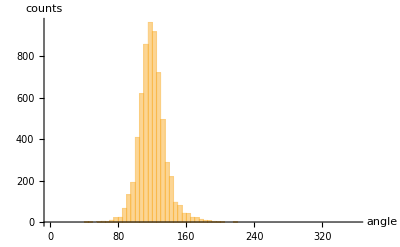

```mathematica
Histogram[{
Flatten[anglesComb,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[anglesComb,1]]
StandardDeviation[Flatten[anglesComb,1]]
```

120.

15.6039

## Domain statistics

## Image 1

Determine the domains alone:

```mathematica
domainIm=Pruning[Pruning@branchImPrun,Infinity]
```

-Graphics-

```mathematica
domains=MorphologicalComponents[ColorNegate@domainIm,"CornerNeighbors"->False];
```

```mathematica
domains//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas=SortBy[ComponentMeasurements[domains,{"Area","Holes"}],Values[#][[1]]&][[;;-4]];
```

```mathematica
domainInds=Keys@domainMeas;
```

```mathematica
Max[dx^2Values[domainMeas][[All,1]]]
```

109.525

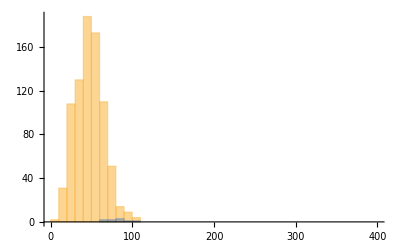

```mathematica
Histogram[{dx^2Select[Values@domainMeas,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas,#[[2]]>=1&][[All,1]]},{0,400,10}]
```

```mathematica
Histogram[{dx^2Select[Values@domainMeas,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas,#[[2]]>=1&][[All,1]]},{0,400,10}]
```

-Graphics-

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds}],#>0&];,b]
```

```mathematica
Max[cornerNumber]
```

9

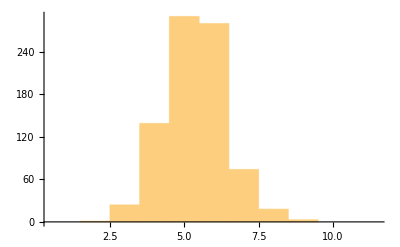

```mathematica
Histogram[cornerNumber,{0.5,12,1}]
```

```mathematica
N@Mean[cornerNumber]
```

5.36671

```mathematica
N@StandardDeviation[cornerNumber]
```

1.05324

## Image 2

Determine the domains alone:

```mathematica
domainIm2=Pruning[Pruning@branchImPrun2,Infinity];
```

```mathematica
domains2=MorphologicalComponents[ColorNegate@domainIm2,"CornerNeighbors"->False];
```

```mathematica
domains2//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas2=SortBy[ComponentMeasurements[domains2,{"Area","Holes"}],Values[#][[1]]&][[;;-2]];
```

```mathematica
domainInds2=Keys@domainMeas2;
```

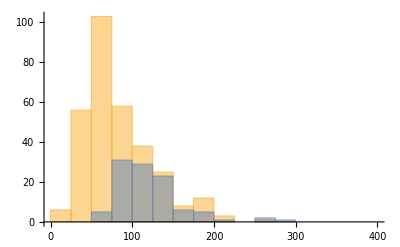

```mathematica
Histogram[{dx^2Select[Values@domainMeas2,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas2,#[[2]]>=1&][[All,1]]},{0,400,25}]
```

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber2=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains2,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints2,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds2}],#>0&];,b]
```

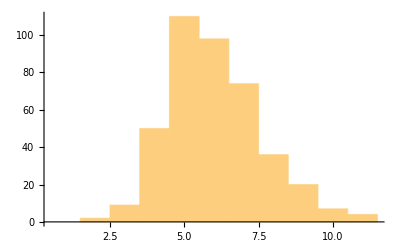

```mathematica
Histogram[cornerNumber2,{0.5,12,1}]
```

```mathematica
N@Mean[cornerNumber2]
```

6.07506

```mathematica
N@StandardDeviation[cornerNumber2]
```

1.70427

## Combined

```mathematica
domainMeasComb=Join[domainMeas,domainMeas2];
cornerNumberComb=Join[cornerNumber,cornerNumber2];
```

```mathematica
Max[dx^2Values[domainMeasComb][[All,1]]]
```

276.927

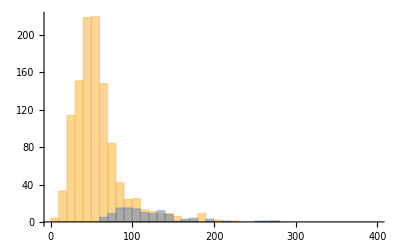

```mathematica
Histogram[{dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]]},{0,400,10}]
```

```mathematica
Mean/@{dx^2Values[domainMeasComb][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]]}
```

{62.7786,57.2925,118.13}

```mathematica
Length@Select[cornerNumberComb,#>10&]
```

7

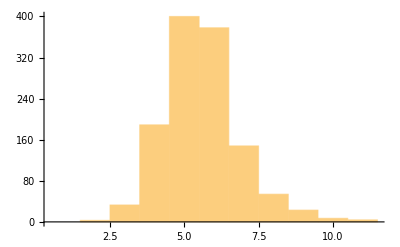

```mathematica
Histogram[cornerNumberComb,{0.5,12,1}]
```

```mathematica
N@Mean[cornerNumberComb]
N@StandardDeviation[cornerNumberComb]
```

5.60225

1.34755